```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/gabrielefranciolini/GitHub_Desktop/SIGW_QCD/Gabriele_Notebooks

## Code

### Preliminaries: import data and solve for the background

```mathematica
Mpl=2435 10^15;
c=299792458 ;(*m/s*)
KinGeV=1/(1160451812 10^-5) 10^-9;
Mpcinm=308568 10^17;
GeVinminv=10^9/(197327 10^-12);
GeVinMpcinv=GeVinminv Mpcinm;
MpcinvinHz=1/Mpcinm c;
yrins=3652422 10^-4 24 60 60;
h2Ωrad = 4.2 10^-5;
HzfrominverseMpc[k_]:=k/(2 π) MpcinvinHz
inverseMpcfromHz[f_]:=(2 π)f/MpcinvinHz
ClearAll[w,cs2,wnT,cs2nT];
w=Interpolation[Join[Import["Data/w_eta.txt","Table"][[1;;77]],Import["Data/w_eta.txt","Table"][[79;;-1]]],InterpolationOrder->1];
cs2=Interpolation[Import["Data/cs2_eta.txt","Table"],InterpolationOrder->1];
wnT[ηn_]:=Piecewise[{{1/3.,ηn<=10^-10/10^-6},{1/3.,ηn>=10^-2/10^-6}},w[ηn 10^-6]]
cs2nT[ηn_]:=Piecewise[{{1/3.,ηn<=10^-10/10^-6},{1/3.,ηn>=10^-2/10^-6}},cs2[ηn  10^-6]]
```

```mathematica
ηin=10^-8.;
(*ηin=10^-4;10^8.48*)
ηout=10^10.;
```

```mathematica
AbsoluteTiming[
solbkg=NDSolve[{
ρ'[η]==-3(1+wnT[η])√((a[η]^2 ρ[η])/3)(*a'[η]/a[η]*)ρ[η],
a'[η] ==√((a[η]^2 ρ[η])/3)a[η],
a[ηin]==1,ρ[ηin]==10^8.477 10^8
},{a[η],ρ[η]},{η,ηin,ηout},MaxSteps->5 10^4];
]
```

{0.180578,Null}

```mathematica
AbsoluteTiming[
solbkg=NDSolve[{
ρ'[η]==(*η Log[10]*)(-3(1+wnT[η])(*η Log[10]*)√((a[η]^2 ρ[η])/3)(*a'[η]/a[η]*)ρ[η]),
a'[η] ==(*η Log[10]*)√((a[η]^2 ρ[η])/3)a[η],
a[Log10[ηin]]==1,ρ[Log10[ηin]]==10^8.477 10^8
},{a[η],ρ[η]},{η,Log10[ηin],Log10[ηout]},MaxSteps->5 10^4];
]
solbkg=NDSolve[{
ρ'[η]==-3(1+wnT[η])a'[η]/a[η] ρ[η],
a'[η]==a[η] √((a[η]^2 ρ[η])/3),
a[ηin]==1,ρ[ηin]==10^8.477 10^8
},{a[η],ρ[η]},{η,ηin,ηout},MaxSteps->5 10^4];
```

{0.050587,Null}

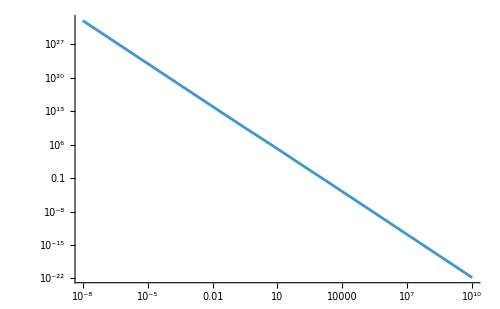

```mathematica
LogLogPlot[(a[η]/.solbkg[[1]]/.{η->ηη})/ηη^4,{ηη,10^-8,10^10},PlotRange->All]
```

```mathematica
solbkg=NDSolve[{
ρ'[η]==-3(1+wnT[η])a'[η]/a[η] ρ[η],
a'[η]==a[η] √((a[η]^2 ρ[η])/3),
a[ηin]==1,ρ[ηin]==10^8.477 10^8
},{a[η],ρ[η]},{η,ηin,ηout},MaxSteps->5 10^4];
asol[ηη_]:=a[η]/.solbkg[[1]]/.{η->ηη}
apsol[ηη_]:=a[η] √((a[η]^2 ρ[η])/3)/.solbkg[[1]]/.{η->ηη}
Hsol[ηη_]:=apsol[ηη]/asol[ηη]
ρsol[ηη_]:=ρ[η]/.solbkg/.{η->ηη}
ClearAll[aF,apF,ρF];
dda=0.01;
aFL=Interpolation[Log10@Table[{η,a[η]/.solbkg[[1]]/.{η->ηη}},{η,10^Range[Log10@ηin,Log10@ηout,dda]}],InterpolationOrder->1];
apFL=Interpolation[Log10@Table[{η,a[η] √((a[η]^2 ρ[η])/3)/.solbkg[[1]]/.{η->ηη}},{η,10^Range[Log10@ηin,Log10@ηout,dda]}],InterpolationOrder->1];
ρFL=Interpolation[Log10@Table[{η,ρ[η]/.solbkg[[1]]/.{η->ηη}},{η,10^Range[Log10@ηin,Log10@ηout,dda]}],InterpolationOrder->1];
wn=Interpolation[Table[{η,wnT[η]/.{η->ηη}},{η,10^Range[Log10@ηin,Log10@ηout,dda]}],InterpolationOrder->1];
cs2n=Interpolation[Table[{η,cs2nT[η]/.{η->ηη}},{η,10^Range[Log10@ηin,Log10@ηout,dda]}],InterpolationOrder->1];
aF[x_]:=10^aFL[Log10@x]
apF[x_]:=10^apFL[Log10@x]
ρF[x_]:=10^ρFL[Log10@x]
HF[ηη_]:=apF[ηη]/aF[ηη]
```

```mathematica
etaofkaH=Interpolation[Table[{(*(1-3wn[η])/2*)HF[η]^2,η},{η,10^Range[Log10@ηin,Log10@ηout,dda]}],InterpolationOrder->1];
```

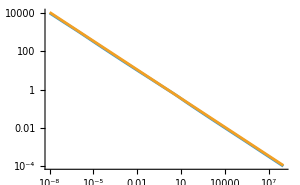

```mathematica
LogLogPlot[{etaofkaH[η], 1.1 η^(-1/2)},{η,10^-8,10^8},ImageSize->300]
```

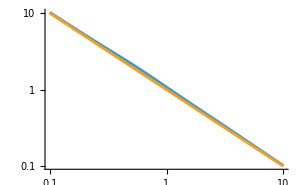

```mathematica
LogLogPlot[{HF[η],η^-1},{η,0.1,10},ImageSize->300]
```

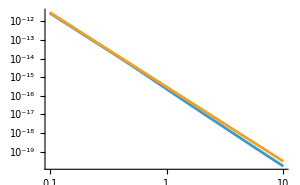

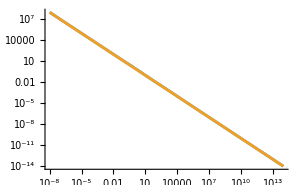

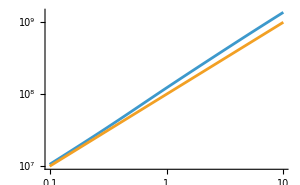

```mathematica
LogLogPlot[{ρF[η],10^-8 10^8.48(η/10^-4)^-4},{η,0.1,10},ImageSize->300] 
LogLogPlot[{apF[η]/aF[η],η^-1},{η,ηin,10^14},ImageSize->300] 
LogLogPlot[{aF[η],10^2 10^6 η},{η,0.1,10},ImageSize->300]
```

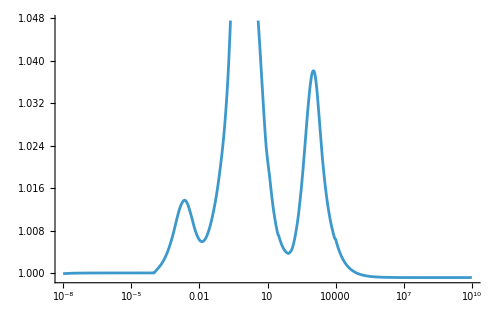

```mathematica
Show[LogLinearPlot[η HF[η],{η, ηin, ηout}]]
```

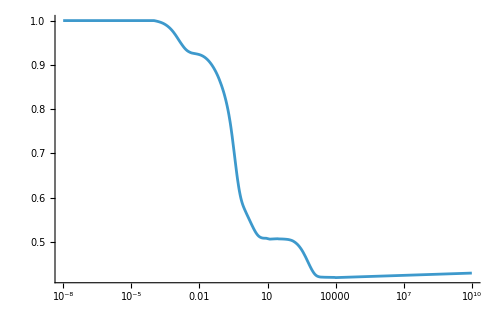

```mathematica
Show[LogLinearPlot[(aF[ηin]^4 ρF[ηin])/(aF[η]^4 ρF[η]),{η, ηin, ηout}]]
```

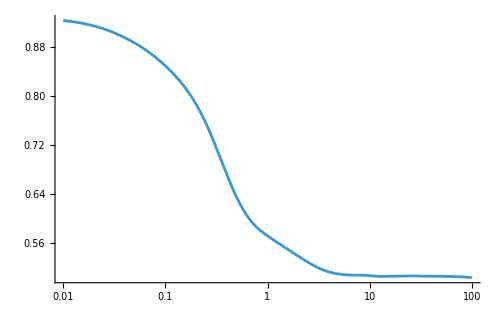

```mathematica
Show[LogLinearPlot[((aF[ηin]HF[ηin])/(aF[η]HF[η]))^2,{η,0.01,100}]]
```

## Code

#### Compute I

```mathematica
ClearAll[term1, term2,term3,term4];
(*term1=Compile[{{ηs,_Real}},(1-3wn[ηs])/2 HF[ηs]^2,RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineIntegerOverflow"->False}];*)
(*term2=Compile[{{ηs,_Real}},3 HF[ηs](1+cs2n[ηs]),RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineIntegerOverflow"->False}];
term3=Compile[{{ηs,_Real}},3 HF[ηs]^2(cs2n[ηs]-wn[ηs]),RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineIntegerOverflow"->False}];
term4=Compile[{{ηs,_Real}},cs2n[ηs],RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineIntegerOverflow"->False}];*)
term1[ηs_]:=(1-3wn[ηs])/2 HF[ηs]^2
term2[ηs_]:=3 HF[ηs](1+cs2n[ηs])
term3[ηs_]:=3 HF[ηs]^2(cs2n[ηs]-wn[ηs])
term4[ηs_]:=cs2n[ηs]
```

#### WKB approximation

```mathematica
ClearAll[ComputePhiWKB];
ComputePhiWKB[k1_,print_]:=Block[{ΦFk1,ΦpFk1,ndsolk1,ϕsol1,mxstpsize=10^7(*10^7 - works for RD*),WP=15(*15 - works for RD*),
ηinI1=10^-2./k1,ηend1=10^3/k1,ηWKB=10^2/k1,
ndsolWKB,ΦFk1WKB,ΦpFk1WKB,tabWKB,WKBsol,S1,A0,Phi0,Pi0,Cplus,Cminus,Phi,etas,intTerm2,intSqrtTerm4,time1,time2,time3
},

time1=AbsoluteTiming[
ndsolk1=Quiet@NDSolve[{
Π'[ηs]+term2[ηs]Π[ηs]+(term4[ηs] k1^2+term3[ηs])Φ[ηs]==0,Φ'[ηs]==Π[ηs],Φ[ηinI1]==1,Π[ηinI1]==0},
{Φ,Π},{ηs,ηinI1,ηend1}
,Method->"StiffnessSwitching"
,PrecisionGoal->WP,AccuracyGoal->WP,WorkingPrecision->WP
,MaxSteps->mxstpsize
][[1]];];
ΦFk1[η_]:=Φ[η]/.ndsolk1;
ΦpFk1[η_]:=Π[η]/.ndsolk1;


time2=AbsoluteTiming[ndsolWKB=Quiet@NDSolve[{
Π'[ηs]+term2[ηs]Π[ηs]+(term4[ηs] k1^2)Φ[ηs]==0,Φ'[ηs]==Π[ηs],
Φ[ηWKB]==ΦFk1[ηWKB],
Π[ηWKB]==ΦpFk1[ηWKB]},
{Φ,Π},{ηs,ηWKB,ηend1},Method->"StiffnessSwitching"
,PrecisionGoal->WP,AccuracyGoal->WP,WorkingPrecision->WP
,MaxSteps->mxstpsize
][[1]];];

ΦFk1WKB[η_]:=Φ[η]/.ndsolWKB;
ΦpFk1WKB[η_]:=Π[η]/.ndsolWKB;

(*Initial conditions*)
Phi0=ΦFk1[ηWKB];Pi0=ΦpFk1[ηWKB];
S1=Sqrt[term4[ηWKB]];A0=1/term4[ηWKB]^(1/4);
Cplus=(Phi0/(2 A0))+(Pi0/(2 I k1 S1 A0));Cminus=(Phi0/(2 A0))-(Pi0/(2 I k1 S1 A0));

(*Define grid for eta*)
etas=10^Range[Log10@ηWKB,Log10@ηend1,(Log10@ηend1-Log10@ηWKB)/10^4];

(*
(* ######## Brute-force approach ######## *)
Phi[eta_]:=Exp[-(1/2) Quiet@NIntegrate[term2[t],{t,ηWKB,eta}]]/term4[eta]^(1/4)*
(Cplus Exp[I k1 Quiet@NIntegrate[Sqrt[term4[t]],{t,ηWKB,eta}]]+Cminus Exp[-I k1 Quiet@NIntegrate[Sqrt[term4[t]],{t,ηWKB,eta}]]);
tabWKB=ParallelTable[{eta,Re@Phi[eta]},{eta,etas}];
*)

(*Precompute cumulative integrals with NDSolveValue*)
time3=AbsoluteTiming[
intTerm2=NDSolveValue[{y'[t]==term2[t],y[ηWKB]==0},y,{t,ηWKB,ηend1}];
intSqrtTerm4=NDSolveValue[{z'[t]==Sqrt[term4[t]],z[ηWKB]==0},z,{t,ηWKB,ηend1}];
];

WKBsol[etas_]:=Exp[-1/2 intTerm2[etas]]/term4[etas]^(1/4)*(Cplus Exp[I k1 intSqrtTerm4[etas]]+Cminus Exp[-I k1 intSqrtTerm4[etas]]);

If[print ==1,
(*Print[LogLogPlot[{Abs[term2[ηs]],Abs[term4[ηs] k1^2],Abs[term3[ηs]]},{ηs,ηinI1,ηend1}]];*)
(*Print[LogLogPlot[{Abs[term2'[ηs]],Abs[cs2n'[ηs] k1^2]},{ηs,ηinI1,ηend1}]];*)
Print[{"time1",time1,"time2",time2,"time3",time3}];

Print[Show[LogLogPlot[{Abs[ΦFk1[ηtt]],10^-1./ηtt^2},{ηtt,ηinI1,ηend1},PlotRange->{{ηinI1, ηend1},{10^-12,10^0}},PlotStyle->{{Black},{Blue}},ImageSize->1000,AspectRatio->1/3]
,LogLogPlot[{Abs[ΦFk1WKB[ηtt]],Abs@WKBsol[ηtt]},{ηtt,ηWKB,ηend1},PlotStyle->{{Red,Dashed},{Cyan}}]]];

Print[Show[LogLogPlot[{Abs[ΦFk1[ηtt]],10^-1./ηtt^2},{ηtt,ηWKB,ηend1},PlotRange->{{ηWKB,ηend1},{10^-12,10^0}},PlotStyle->{{Black},{Blue}},ImageSize->10000,AspectRatio->1/30]
,LogLogPlot[{Abs[ΦFk1WKB[ηtt]],Abs@WKBsol[ηtt]},{ηtt,ηWKB,ηend1},PlotStyle->{{Red,Dashed},{Cyan}}]]];

Print[LogLogPlot[{Abs[ΦFk1[ηtt]/WKBsol[ηtt]]},{ηtt,ηWKB,ηend1},PlotRange->{{ηWKB, ηend1},{10^-2,10^2}},GridLines->{{},{1}},PlotStyle->{{Black},{Blue}}]];
];

]
```

{time1,{2.67656,Null},time2,{0.912639,Null},time3,{0.004048,Null}}

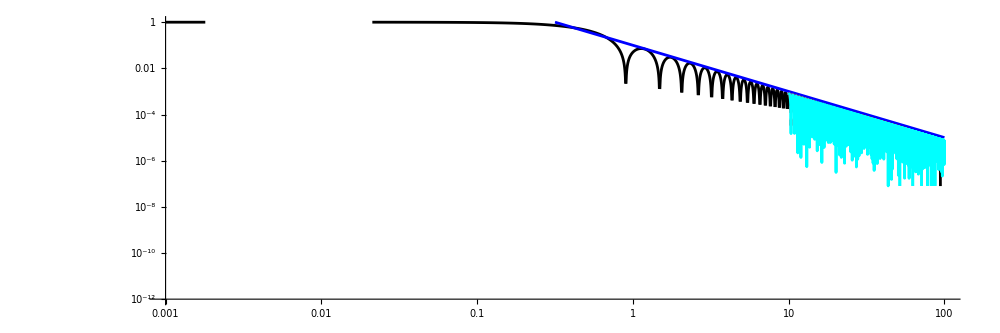

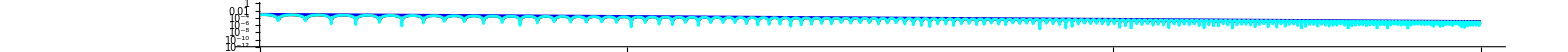

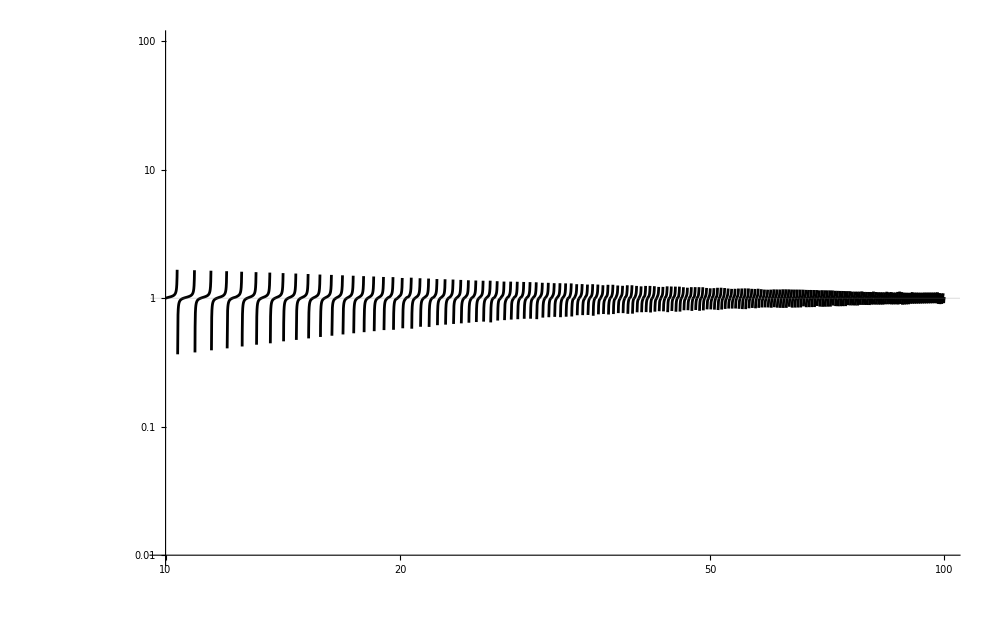

{4.66286,Null}

```mathematica
AbsoluteTiming[ComputePhiWKB[10,1]]
```

```mathematica
Computeg[k_,print_]:=Block[{g1k,g2k,G1k,G2k,ndsolg2,ndsolg1,mxstpsize=10^7(*10^7 - works for RD*),WP=15(*15 - works for RD*),
ηinI=10^-2./k,ηend=10^3/k,ηWKB=10^2/k,
intSqrtKminusTerm1,g10,G10,g20,G20,S1,A1,C1plus,C1minus,g1WKB,G1WKB,C2plus,C2minus,g2WKB,G2WKB
},

ndsolg1=Quiet@NDSolve[{G1'[ηs]+(k^2-term1[ηs])g1[ηs]==0,g1'[ηs]==G1[ηs],g1[ηinI]==0,G1[ηinI]==1},{g1,G1},{ηs,ηinI,ηend}
,Method->"StiffnessSwitching"(*,PrecisionGoal->WP,AccuracyGoal->WP,WorkingPrecision->WP,MaxSteps->mxstpsize*)][[1]];
ndsolg2=Quiet@NDSolve[{G2'[ηs]+(k^2-term1[ηs])g2[ηs]==0,g2'[ηs]==G2[ηs],g2[ηinI]==1,G2[ηinI]==0},{g2,G2},{ηs,ηinI,ηend}
,Method->"StiffnessSwitching"(*,PrecisionGoal->WP,AccuracyGoal->WP,WorkingPrecision->WP,MaxSteps->mxstpsize*)][[1]];
g1k[η_]:=g1[η]/. ndsolg1;
G1k[η_]:=G1[η]/. ndsolg1;
g2k[η_]:=g2[η]/. ndsolg2;
G2k[η_]:=G2[η]/. ndsolg2;

intSqrtKminusTerm1=NDSolveValue[{z'[t]==Sqrt[(k^2-term1[t])/k^2],z[ηWKB]==0},z,{t,ηWKB,ηend}];
g10=g1k[ηWKB];G10=G1k[ηWKB];g20=g2k[ηWKB];G20=G2k[ηWKB];
     
S1=Sqrt[(k^2-term1[ηWKB])/k^2];
A1=((k^2-term1[ηWKB])/k^2)^(-1/4);
C1plus=(g10/(2 A1))+(G10/(2 I k S1 A1));
C1minus=(g10/(2 A1))-(G10/(2 I k S1 A1));

g1WKB[η_]:=((k^2-term1[η])/k^2)^(-1/4)*(C1plus Exp[I k intSqrtKminusTerm1[η]]+C1minus Exp[-I k intSqrtKminusTerm1[η]]);
G1WKB[η_]:=D[g1WKB[x],x]/. x->η; 

C2plus=(g20/(2 A1))+(G20/(2 I k S1 A1));
C2minus=(g20/(2 A1))-(G20/(2 I k S1 A1));

g2WKB[η_]:=((k^2-term1[η])/k^2)^(-1/4)*(C2plus Exp[I k intSqrtKminusTerm1[η]]+C2minus Exp[-I k intSqrtKminusTerm1[η]]);
G2WKB[η_]:=D[g2WKB[x],x]/. x->η;

If[print==1,
Print[LogLogPlot[{
Abs[g1k[ηplot]],
Abs[g1WKB[ηplot]]
},{ηplot,ηWKB,ηend},ImageSize->300,
(*PlotRange->{All,{10^-20,10^10}},*)
PlotStyle->{{Black},{Red, Dashed},{Dashed},{Dashed}}]];
Print[LogLogPlot[{
Abs[g2k[ηplot]],
Abs[g2WKB[ηplot]]
},{ηplot,ηWKB,ηend},ImageSize->300,
(*PlotRange->{All,{10^-20,10^10}},*)
PlotStyle->{{Black},{Red, Dashed},{Dashed},{Dashed}}]];

];

]
```

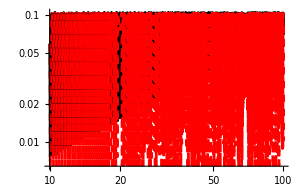

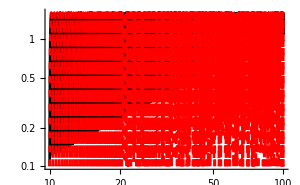

```mathematica
Computeg[10,1]
```

```mathematica
ClearAll[ComputePhiWKB];
ComputeI[k1_,k2_,k_,print_]:=Block[{ΦFk1,ΦpFk1,ndsolk1,ΦFk2,ΦpFk2,ndsolk2,g1k,g2k,G1k,G2k,ndsolg2,ndsolg1,mxstpsize=10^7(*10^7 - works for RD*),WP=15(*15 - works for RD*),
ηinI1=10^-2./k1,ηend1=10^3/k1,ηWKB1=10^2/k1,
ηinI2=10^-2./k2,ηend2=10^3/k2,ηWKB2=10^2/k2,
ηinI=10^-2./k,ηend=10^3/k,ηWKB=10^2/k,
WKBsol1,WKBsol1prime,S11,A01,Phi10,Pi10,Cplus1,Cminus1,
WKBsol2,WKBsol2prime,S12,A02,Phi20,Pi20,Cplus2,Cminus2,
Phi,etas,intTerm21,intSqrtTerm41,intTerm22,intSqrtTerm42,
intSqrtKminusTerm1,g10,G10,g20,G20,S1,A1,C1plus,C1minus,C2plus,C2minus,g1WKB,G1WKB,g2WKB,G2WKB
},
ndsolk1=Quiet@NDSolve[{Π'[ηs]+term2[ηs]Π[ηs]+(term4[ηs] k1^2+term3[ηs])Φ[ηs]==0,Φ'[ηs]==Π[ηs],Φ[ηinI1]==1,Π[ηinI1]==0},
{Φ,Π},{ηs,ηinI1,ηend1},Method->"StiffnessSwitching"
(*,PrecisionGoal->WP,AccuracyGoal->WP,WorkingPrecision->WP
,MaxSteps->mxstpsize*)][[1]];
ΦFk1[η_]:=Φ[η]/.ndsolk1;
ΦpFk1[η_]:=Π[η]/.ndsolk1;

ndsolk2=Quiet@NDSolve[{Π'[ηs]+term2[ηs]Π[ηs]+(term4[ηs] k2^2+term3[ηs])Φ[ηs]==0,Φ'[ηs]==Π[ηs],Φ[ηinI2]==1,Π[ηinI2]==0},
{Φ,Π},{ηs,ηinI2,ηend2},Method->"StiffnessSwitching"
(*,PrecisionGoal->WP,AccuracyGoal->WP,WorkingPrecision->WP
,MaxSteps->mxstpsize*)][[1]];
ΦFk2[η_]:=Φ[η]/.ndsolk2;
ΦpFk2[η_]:=Π[η]/.ndsolk2;

ndsolg1=Quiet@NDSolve[{G1'[ηs]+(k^2-term1[ηs])g1[ηs]==0,g1'[ηs]==G1[ηs],g1[ηinI]==0,G1[ηinI]==1},{g1,G1},{ηs,ηinI,ηend}
,Method->"StiffnessSwitching"(*,PrecisionGoal->WP,AccuracyGoal->WP,WorkingPrecision->WP,MaxSteps->mxstpsize*)][[1]];
ndsolg2=Quiet@NDSolve[{G2'[ηs]+(k^2-term1[ηs])g2[ηs]==0,g2'[ηs]==G2[ηs],g2[ηinI]==1,G2[ηinI]==0},{g2,G2},{ηs,ηinI,ηend}
,Method->"StiffnessSwitching"(*,PrecisionGoal->WP,AccuracyGoal->WP,WorkingPrecision->WP,MaxSteps->mxstpsize*)][[1]];
g1k[η_]:=g1[η]/. ndsolg1;
G1k[η_]:=G1[η]/. ndsolg1;
g2k[η_]:=g2[η]/. ndsolg2;
G2k[η_]:=G2[η]/. ndsolg2;


Phi10=ΦFk1[ηWKB1];Pi10=ΦpFk1[ηWKB1];
S11=Sqrt[term4[ηWKB1]];A01=1/term4[ηWKB1]^(1/4);
Cplus1=(Phi10/(2 A01))+(Pi10/(2 I k1 S11 A01));Cminus1=(Phi10/(2 A01))-(Pi10/(2 I k1 S11 A01));
intTerm21=NDSolveValue[{y'[t]==term2[t],y[ηWKB1]==0},y,{t,ηWKB1,ηend1}];
intSqrtTerm41=NDSolveValue[{z'[t]==Sqrt[term4[t]],z[ηWKB1]==0},z,{t,ηWKB1,ηend1}];
WKBsol1[etas_]:=Exp[-1/2 intTerm21[etas]]/term4[etas]^(1/4)*(Cplus1 Exp[I k1 intSqrtTerm41[etas]]+Cminus1 Exp[-I k1 intSqrtTerm41[etas]]);
WKBsol1prime[etas_]:=1/(4 term4[etas]^(5/4))ⅇ^(-ⅈ k1 intSqrtTerm41[etas]-intTerm21[etas]/2) (-4 ⅈ (Cminus1-Cplus1 ⅇ^(2 ⅈ k1 intSqrtTerm41[etas])) k1 term4[etas] intSqrtTerm41'[etas]-2 (Cminus1+Cplus1 ⅇ^(2 ⅈ k1 intSqrtTerm41[etas])) term4[etas] intTerm21'[etas]-(Cminus1+Cplus1 ⅇ^(2 ⅈ k1 intSqrtTerm41[etas])) term4'[etas]);


Phi20=ΦFk2[ηWKB2];Pi20=ΦpFk2[ηWKB2];
S12=Sqrt[term4[ηWKB2]];A02=1/term4[ηWKB2]^(1/4);
Cplus2=(Phi20/(2 A02))+(Pi20/(2 I k2 S12 A02));Cminus2=(Phi20/(2 A02))-(Pi20/(2 I k2 S12 A02));
intTerm22=NDSolveValue[{y'[t]==term2[t],y[ηWKB2]==0},y,{t,ηWKB2,ηend2}];
intSqrtTerm42=NDSolveValue[{z'[t]==Sqrt[term4[t]],z[ηWKB2]==0},z,{t,ηWKB2,ηend2}];
WKBsol2[etas_]:=Exp[-1/2 intTerm22[etas]]/term4[etas]^(1/4)*(Cplus2 Exp[I k2 intSqrtTerm42[etas]]+Cminus2 Exp[-I k2 intSqrtTerm42[etas]]);
WKBsol2prime[etas_]:=1/(4 term4[etas]^(5/4))ⅇ^(-ⅈ k2 intSqrtTerm42[etas]-intTerm22[etas]/2) (-4 ⅈ (Cminus2-Cplus2 ⅇ^(2 ⅈ k2 intSqrtTerm42[etas])) k2 term4[etas] intSqrtTerm42'[etas]-2 (Cminus2+Cplus2 ⅇ^(2 ⅈ k2 intSqrtTerm42[etas])) term4[etas] intTerm22'[etas]-(Cminus2+Cplus2 ⅇ^(2 ⅈ k2 intSqrtTerm42[etas])) term4'[etas]);
intSqrtKminusTerm1=NDSolveValue[{z'[t]==Sqrt[(k^2-term1[t])/k^2],z[ηWKB]==0},z,{t,ηWKB,ηend}];

g10=g1k[ηWKB];G10=G1k[ηWKB];g20=g2k[ηWKB];G20=G2k[ηWKB];
S1=Sqrt[(k^2-term1[ηWKB])/k^2];
A1=((k^2-term1[ηWKB])/k^2)^(-1/4);
C1plus=(g10/(2 A1))+(G10/(2 I k S1 A1));
C1minus=(g10/(2 A1))-(G10/(2 I k S1 A1));

g1WKB[η_]:=((k^2-term1[η])/k^2)^(-1/4)*(C1plus Exp[I k intSqrtKminusTerm1[η]]+C1minus Exp[-I k intSqrtKminusTerm1[η]]);
G1WKB[η_]:=D[g1WKB[x],x]/. x->η; 

C2plus=(g20/(2 A1))+(G20/(2 I k S1 A1));
C2minus=(g20/(2 A1))-(G20/(2 I k S1 A1));

g2WKB[η_]:=((k^2-term1[η])/k^2)^(-1/4)*(C2plus Exp[I k intSqrtKminusTerm1[η]]+C2minus Exp[-I k intSqrtKminusTerm1[η]]);
G2WKB[η_]:=D[g2WKB[x],x]/. x->η;






(*Print[{g1k[ηWKB1],g2k[ηWKB1],ΦFk1[ηWKB1],ΦFk2[ηWKB1]}];*)
If[print==1,
Print[LogLogPlot[{Abs[ΦFk1[ηtt]/WKBsol1[ηtt]],Abs[ΦFk2[ηtt]/WKBsol2[ηtt]]},{ηtt,ηWKB,ηend1},PlotRange->{{ηWKB, ηend1},{10^-2,10^2}},GridLines->{{},{1}},PlotStyle->{{Black},{Blue}},AspectRatio->1/4]];
Print[LogLogPlot[{
Abs[g1WKB[ηplot]/g1k[ηplot]-1],Abs[g2WKB[ηplot]/g2k[ηplot]-1]
},{ηplot,ηWKB,ηend1},
(*PlotRange->{All,{10^-20,10^10}},*)
PlotStyle->{{Black},{Red, Dashed},{Dashed},{Dashed}},AspectRatio->1/4]];
Print[LogLogPlot[{
Abs[(k^2/aF[ηend] aF[ηtt]g1k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt])))],
Abs[(k^2/aF[ηend] aF[ηtt]g2k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt])))]
},{ηtt,ηinI,ηend},(*PlotRange->{All,{10^-20,10^10}},*)PlotStyle->{{},{},{Dashed},{Dashed}},
GridLines->{{ηinI1,ηinI2,ηinI,ηWKB,ηWKB1,ηWKB2},{}}]];
(*Print[LogLogPlot[{
Re[ηtt(k^2/aF[ηend] aF[ηtt]g1k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt])))],
Re[ηtt(k^2/aF[ηend] aF[ηtt]g2k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt])))]
},{ηtt,ηinI,ηend},(*PlotRange->{All,{10^-20,10^10}},*)PlotStyle->{{},{},{Dashed},{Dashed}}]];
Print[LogLogPlot[{
Im[ηtt(k^2/aF[ηend] aF[ηtt]g1k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt])))],
Im[ηtt(k^2/aF[ηend] aF[ηtt]g2k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt])))]
},{ηtt,ηinI,ηend},(*PlotRange->{All,{10^-20,10^10}},*)PlotStyle->{{},{},{Dashed},{Dashed}}]];
Print[LogLogPlot[{
D[Arg[ηtt(k^2/aF[ηend] aF[ηtt]g1k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt])))],ηtt]/.{ηtt->ηtt2},
D[Arg[ηtt(k^2/aF[ηend] aF[ηtt]g2k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt])))],ηtt]/.{ηtt->ηtt2}
},{ηtt2,ηinI,ηend},(*PlotRange->{All,{10^-20,10^10}},*)PlotStyle->{{},{},{Dashed},{Dashed}}]];*)
];

(*Eq. C1*)
(*Print[Table[{ηtt,ηtt(k^2/aF[ηend] aF[ηtt]g1k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt])))},{ηtt,10^Range[Log10@ηinI,Log10@ηend,(Log10@ηend-Log10@ηinI)/10]}]];*)
Print[{"I1",NIntegrate[(k^2/aF[ηend] aF[ηtt]g1k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt]))),{ηtt,ηinI,ηend}]}];
Print[{"I2",NIntegrate[(k^2/aF[ηend] aF[ηtt]g2k[ηtt](2ΦFk1[ηtt] ΦFk2[ηtt]+4/(3(1+wn[ηtt]))(ΦFk1[ηtt]+ΦpFk1[ηtt]/HF[ηtt])(ΦFk2[ηtt]+ΦpFk2[ηtt]/HF[ηtt]))),{ηtt,ηinI,ηend}]}];



]
```

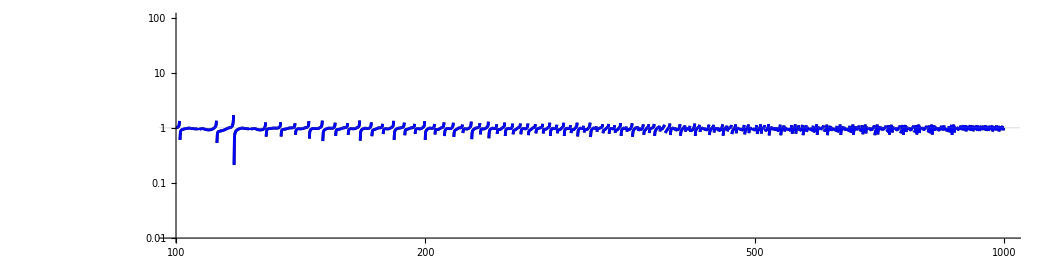

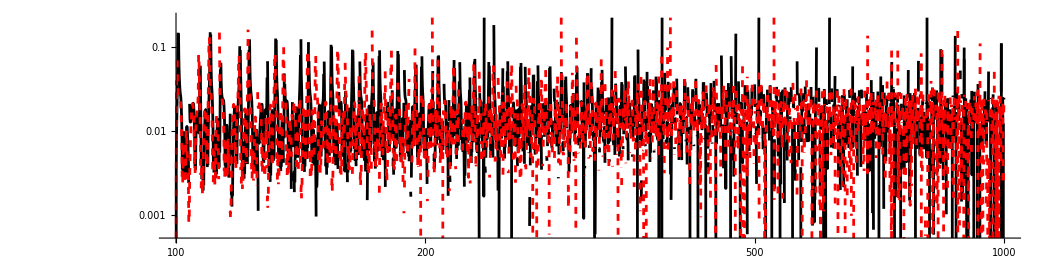

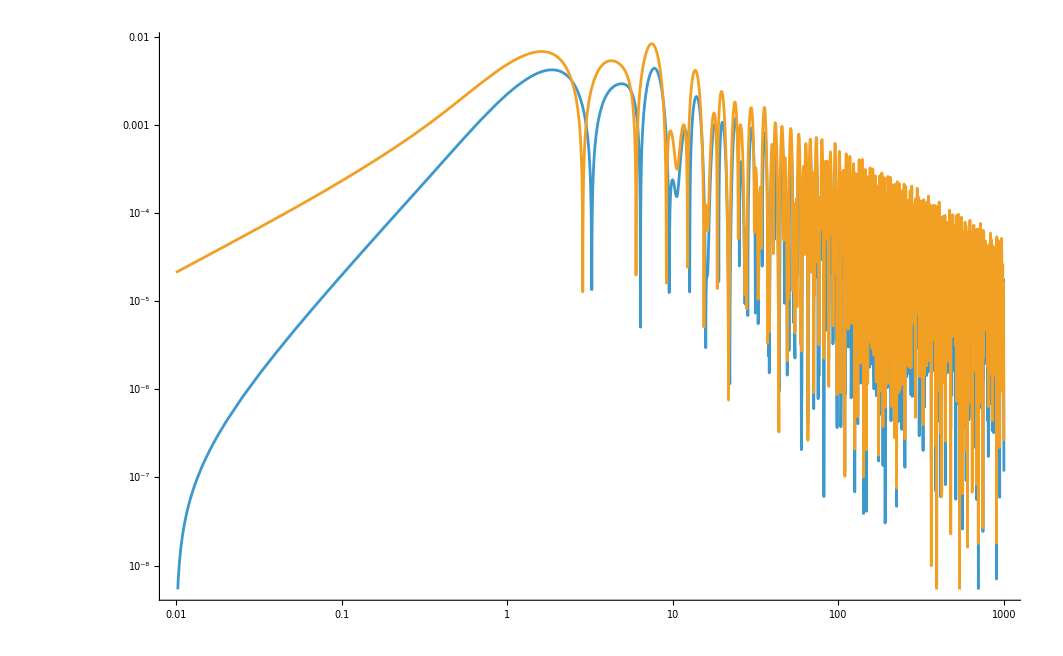

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ηtt near {ηtt} = {80.0718}. NIntegrate obtained 0.00825091 and 0.0000150186 for the integral and error estimates.

{I1,0.00825091}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ηtt near {ηtt} = {64.4469}. NIntegrate obtained 0.0171933 and 0.0000256618 for the integral and error estimates.

{I2,0.0171933}

```mathematica
ComputeI[1,1,1,1]
```

```mathematica
a
```

```mathematica
time2=AbsoluteTiming[ndsolWKB=Quiet@NDSolve[{
Π'[ηs]+term2[ηs]Π[ηs]+(term4[ηs] k1^2)Φ[ηs]==0,Φ'[ηs]==Π[ηs],
Φ[ηWKB]==ΦFk1[ηWKB],
Π[ηWKB]==ΦpFk1[ηWKB]},
{Φ,Π},{ηs,ηWKB,ηend1},Method->"StiffnessSwitching"
,PrecisionGoal->WP,AccuracyGoal->WP,WorkingPrecision->WP
,MaxSteps->mxstpsize
][[1]];];

ΦFk1WKB[η_]:=Φ[η]/.ndsolWKB;
ΦpFk1WKB[η_]:=Π[η]/.ndsolWKB;

(*Here WKB approximation Initial conditions*)
Phi0=ΦFk1[ηWKB];Pi0=ΦpFk1[ηWKB];
S1=Sqrt[term4[ηWKB]];A0=1/term4[ηWKB]^(1/4);
Cplus=(Phi0/(2 A0))+(Pi0/(2 I k1 S1 A0));Cminus=(Phi0/(2 A0))-(Pi0/(2 I k1 S1 A0));

time3=AbsoluteTiming[
intTerm2=NDSolveValue[{y'[t]==term2[t],y[ηWKB]==0},y,{t,ηWKB,ηend1}];
intSqrtTerm4=NDSolveValue[{z'[t]==Sqrt[term4[t]],z[ηWKB]==0},z,{t,ηWKB,ηend1}];
];

WKBsol[etas_]:=Exp[-1/2 intTerm2[etas]]/term4[etas]^(1/4)*(Cplus Exp[I k1 intSqrtTerm4[etas]]+Cminus Exp[-I k1 intSqrtTerm4[etas]]);
```

```mathematica
I1=4/9 k^2/aF[ηend] Quiet@NIntegrate[(aF[ηtt]g1k(2ΦFk1 ΦFk2+4/(3(1+wn[ηtt]))(ΦFk1+ΦFpk1/HF[ηtt])(ΦFk2+ΦFpk2/HF[ηtt]))),{ηtt,ηinI,ηend},Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->20,PrecisionGoal->20,AccuracyGoal->20];
I2=4/9 k^2/aF[ηend] Quiet@NIntegrate[(aF[ηtt]g2k(2ΦFk1 ΦFk2+4/(3(1+wn[ηtt]))(ΦFk1+ΦFpk1/HF[ηtt])(ΦFk2+ΦFpk2/HF[ηtt]))),{ηtt,ηinI,ηend},Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->20,PrecisionGoal->20,AccuracyGoal->20];
```